## The construction of Richman’s EoS

Yi Yin

Abstract

We will construct an E.o.S with a critical point.  We will read in the parameters from the same parameter file that the c++ code uses, params.txt.  We will then create the E.o.S. file and directory structure that the c++ code needs to run.

(Copyright information: Notebook template created by Steven S. Gubser
  https://www.princeton.edu/physics/research/high-energy-theory/gubser-group/code-repository/like-latex/
Copies and adaptations of this template must include this URL in full.)

## Documentation for the construction of EoS

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/gregoryridgway/Desktop/Heavy_Ion/SimulatingHydroPlus/EOS

We will simply add QGP-like EoS to critical EoS

We set T_c=1 at this moment. It is useful to define

A=ξ^-2

c_V=aL T^3, T<T_Low;

c_V=aH T^3, T>T_High;

We should keep in mind that T_Low~1-ΔT. Otherwise, further refinements are needed.

Add a baseline value for the coefficient of T^3 term for QGP

```mathematica
Nf = 2;
Clear[aQGP];aQGP=36(32+21Nf)/180;
```

```mathematica
<<./package/presentation.m
```

## Sample results

Input parameters

```mathematica
paramList = StringCases[#,x:NumberString:>ToExpression[x]]⟦1⟧&/@(ReadList["../params.txt",String]⟦2;;;;2⟧);
```

```mathematica
Clear[ΔT,ξmax,TLow,THigh,aL,aH];
{ΔT,ξmax,TLow,THigh}=paramList⟦{-4,-3,-2,-1}⟧
{aL,aH}={1,1}aQGP;
ξmaxnow=ξmax;
ΔT0=ΔT;
```

{0.1,1.,0.9,1.1}

```mathematica
<<./package/Construct_EoS.m
```

#### Plot c_V

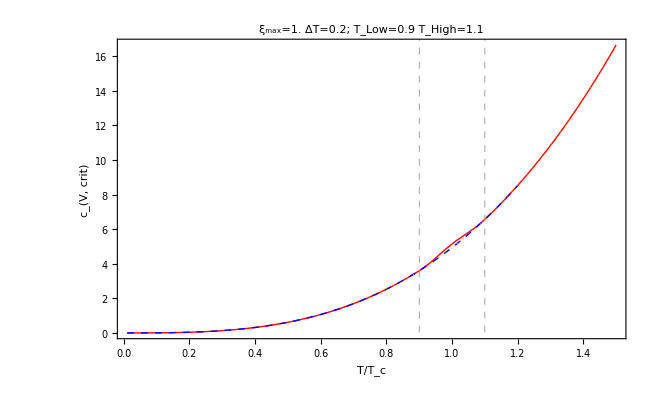

```mathematica
Show[cVPlot]
```

#### Plot ϵ vs T and p vs T and s vs T

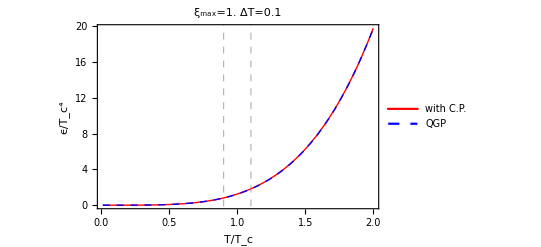

```mathematica
Show[ϵPlot]
```

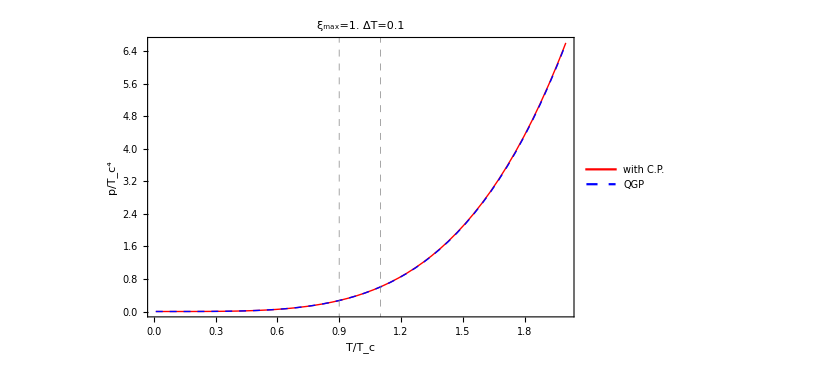

```mathematica
Show[pPlot]
```

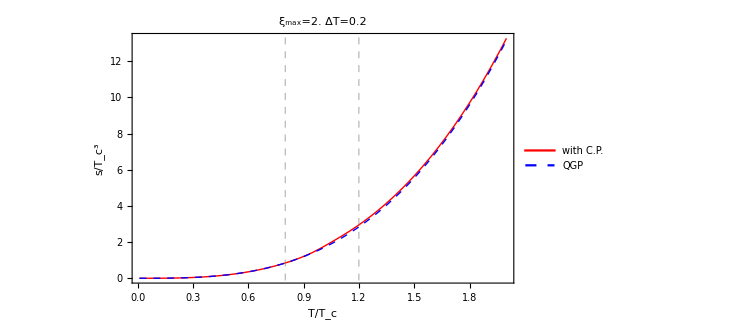

```mathematica
Show[sPlot]
```

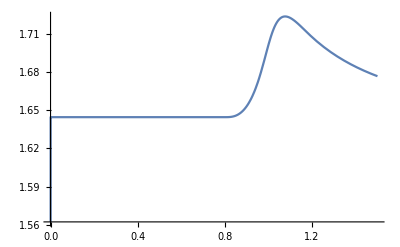

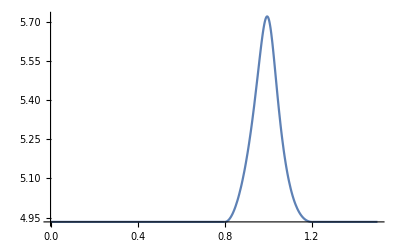

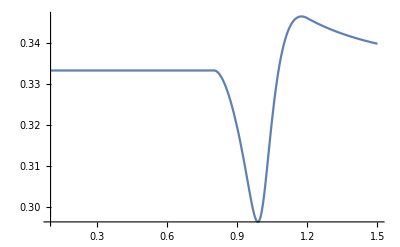

```mathematica
Plot[sFull[T]/T^3,{T,0,1.5}]
Plot[cVfun[T]/T^3,{T,0,1.5},PlotRange->All]
Plot[sFull[T]/cVfun[T],{T,0.1,1.5},PlotRange->All]
```

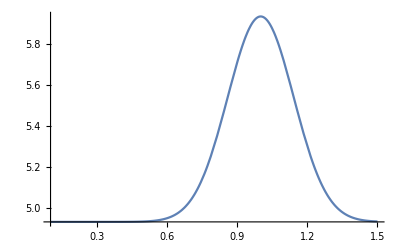

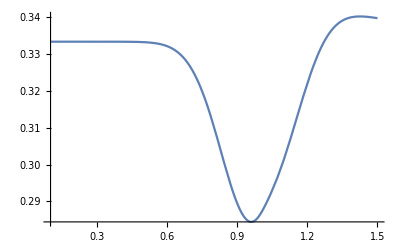

```mathematica
Plot[aL/3 + Exp[(-(T-1)^2)/(ΔT^2)],{T,0.1,1.5},PlotRange->Full]
Plot[(sFull[T]/T^3)/(aL/3 + Exp[(-(T-1)^2)/(ΔT^2)]),{T,0.1,1.5},PlotRange->Full]
```

#### Plot (c^2)_s vs T

1. This low temperature cusp seems to be causing the  discontinuity in c^2

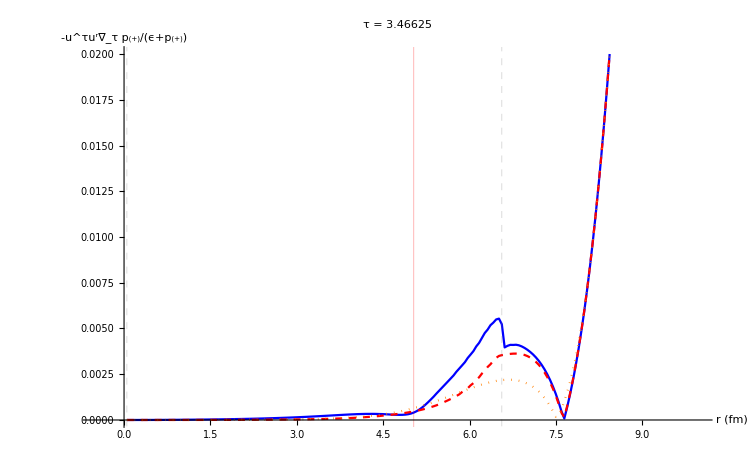

Critical

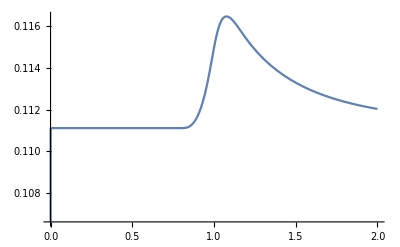

```mathematica
Plot[sFull[t]/((aL+(aH-aL)*(.5+ArcTan[(t-1)/ΔT]/π))t^3),{t,0,2}]
```

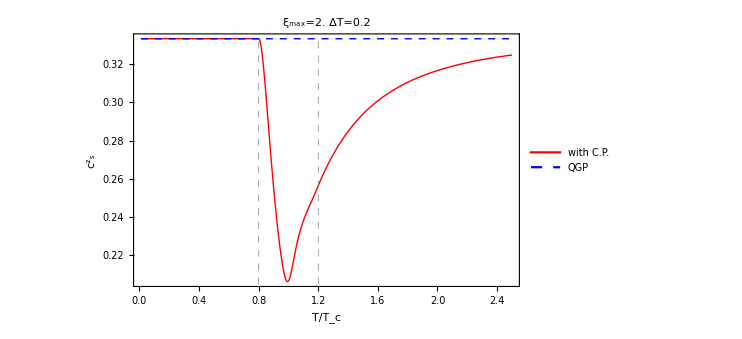

```mathematica
Show[cs2Plot]
```

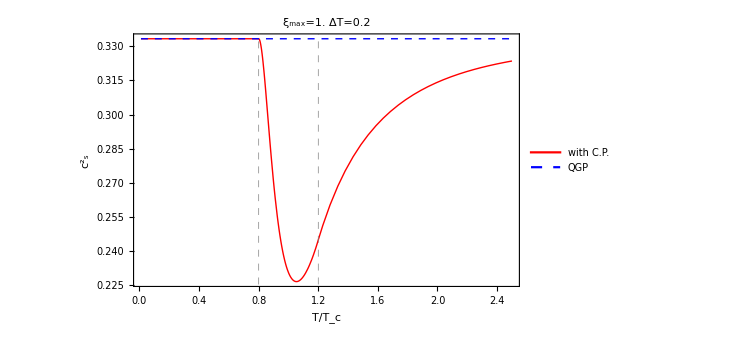
```mathematica
Show[-Graphics-,-Graphics-]
```

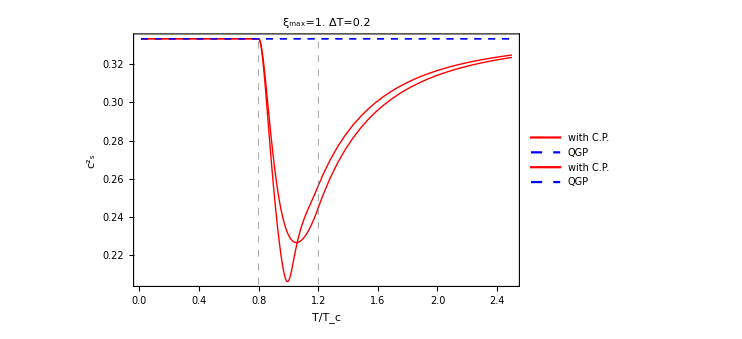

No CP

```mathematica
Show[cs2Plot]
```

-Graphics-

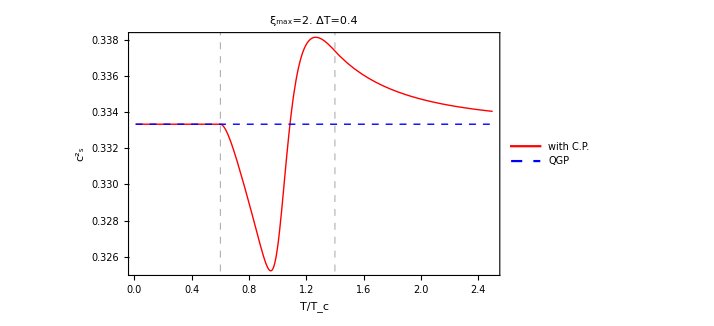

```mathematica
Show[cs2Plot]
```

#### Plot ξ vs T

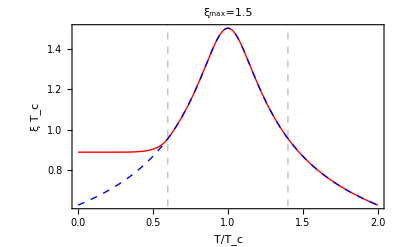

```mathematica
Show[ξPlot]
```

Export to c++ input file

We must define the first and second derivatives of ξ with respect to ϵ

```mathematica
-ALowdϵ[1.5]
```

84.1288

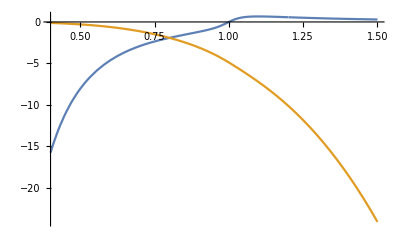

```mathematica
Plot[{AfundT[T,ΔT,ξmax](1/cVfun[T]),d2Now ϵFull[T]},{T,0.4,1.5},PlotRange->All]
```

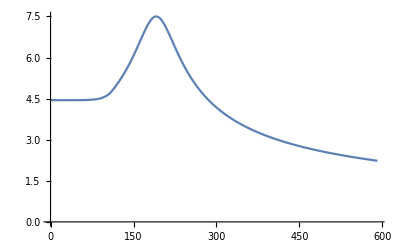

```mathematica
ListLinePlot[xis]
```

-Graphics-

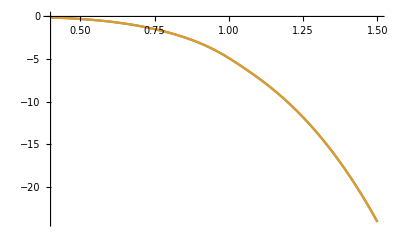

```mathematica
Plot[{AfundT[T,ΔT,ξmax](1/cVfun[T]),d2Now ϵFull[T]},{T,.4,1.5}]
Plot[{ALowdϵ[T]},{T,.4,1.5}]
(*Plot[AfunFulldϵ[T],{T,.4,1.5}]*)
```

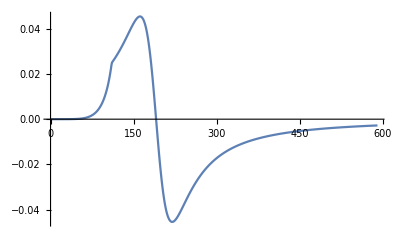

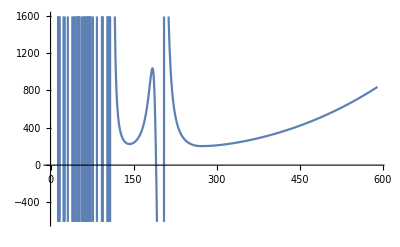

```mathematica
tmp=Table[Afun[tm/tc,ΔT,ξmax],{tm,ran}];
ListLinePlot[Differences[xis]]
ListLinePlot[Differences[tmp^(-1/2)/tc]/Differences[es](*,PlotRange->All*)]
```

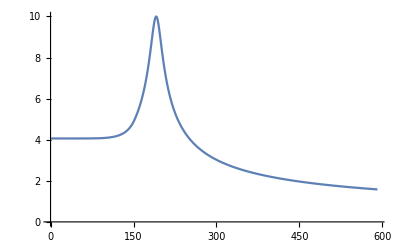

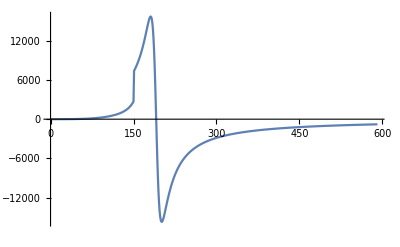

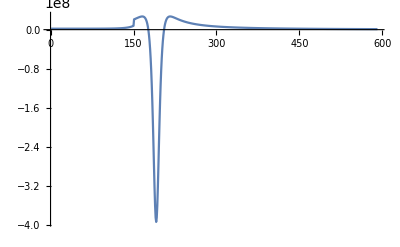

```mathematica
ListLinePlot[xis]
ListLinePlot[dXis,PlotRange->All]
ListLinePlot[d2Xi,PlotRange->All]
```

-Graphics-

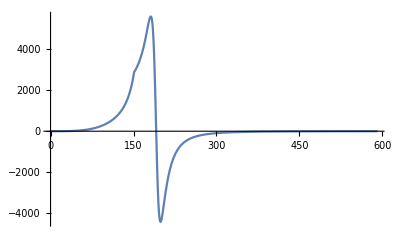

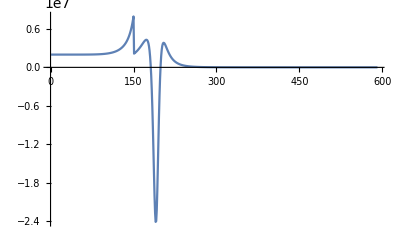

```mathematica
ListLinePlot[xis]
ListLinePlot[dXis,PlotRange->All]
ListLinePlot[d2Xi,PlotRange->All]
```

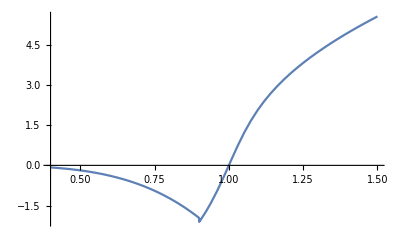

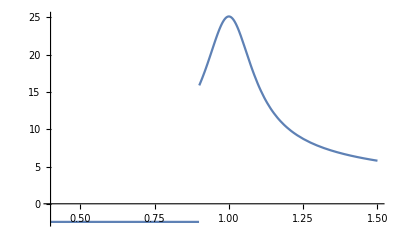

```mathematica
Plot[AfunFulldϵ[t],{t,.4,1.5}]
Plot[AfunFulldϵ2[t],{t,.4,1.5}]
```

```mathematica
dxifun[t_]:= -1/2(AfunFull[t])^(-3/2)*AfunFulldϵ[t];
d2xifun[t_]:= 3/4(AfunFull[t])^(-5/2)*AfunFulldϵ[t]^2-1/2(AfunFull[t])^(-3/2)*AfunFulldϵ2[t];
```

We then choose a critical temperature and form a list of T,ϵ, p, c^2, ξ, dξ/dϵ,(d^2 ξ)/dϵ^2, c_v (heat capacity is obsolete).

```mathematica
tc = paramList⟦-7⟧;
ran=Range[.01,.6,.001];
Length[ran]
es=(ϵFull[#]/#^4)&/@(ran/tc);
ps=(pFull[#]/#^4)&/@(ran/tc);
cs=(cs2Full[#])&/@(ran/tc);
(*cs=((sFull[#]/#^3)/(aL/3 + Exp[(-(#-1)^2)/(ΔT^2)]))&/@(ran/tc);*)
xis=((AfunFull[#])^(-1/2)/tc)&/@(ran/tc);
dXis=(dxifun[#]/tc^5)&/@(ran/tc);
d2Xi=(d2xifun[#]/tc^9)&/@(ran/tc);
```

591

Then we create two directories to which the c++ code will output whenever it uses these parameters.  Afterwards, we create the EOS file that will be formatted correctly

```mathematica
t0=0.2;
```

```mathematica
SciNot[num_]:=Block[{exp=Floor[Log10[num]], dig=0,  remain=0},
dig=Floor[num/10^exp];
remain=num/10^exp-dig ;
If [remain== 0,
Return[ToString[dig]<>"e"<>ToString[exp]],
Return[ToString[dig]<>"."<>StringSplit[
ToString[remain],"."]⟦-1⟧
<>"e"<>ToString[exp]]
]
]

Concat[strings_,nums_]:=StringJoin@Flatten@Transpose[{
strings,SciNot/@nums
}]
str = Concat[{"_Tc_","_aL_", "_aH_", "_dT_","_Xm_","_TL_","_TH_"},{t0,aL/aQGP,aH/aQGP,ΔT,ξmax,TLow,THigh}];

dir = "../../data/snapshot/"<>StringTake[str,{2,-1}];
(*If I haven't already created a directory with this equation of state, make one*)
If[FileNames[dir]=={},
CreateDirectory[dir<>"/with_backreaction"];
CreateDirectory[dir<>"/without_backreaction"];
]
data=Transpose[SetPrecision[{ran,es,ps,cs,xis, dXis,d2Xi},7]];
Export["../EOS/richEOS"<>str<>".dat",Prepend[data,{496}]]
```

../EOS/richEOS_Tc_2e-1_aL_1e0_aH_1e0_dT_1e-1_Xm_1e0_TL_9e-1_TH_1.1e0.dat